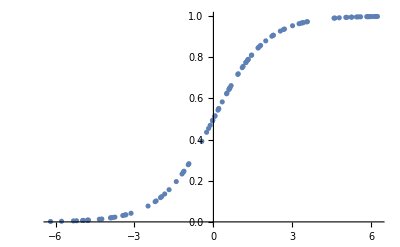

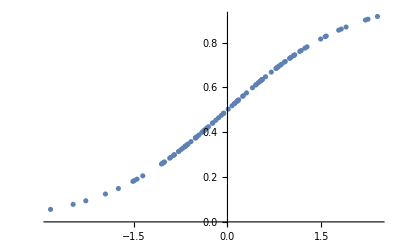

```mathematica
<<NeuralNetworks`;
n = 100;
x = RandomReal[{-2*π, 2*π}, n];
𝒫=WhiteNoiseProcess[];
xx = RandomVariate[NormalDistribution[0,1],100];
y = Evaluate[LogisticSigmoid[x]];
yy = Evaluate[LogisticSigmoid[xx]];
data = Transpose@{x,y};
data2 = Transpose@{xx,yy};
ListPlot[data]
ListPlot[data2]
```